```mathematica
V = ReadList["harmonic-x.dat",{Number,Number}]
```

{{-10.,-10.},{-9.,-9.},{-8.,-8.},{-7.,-7.},{-6.,-6.},{-5.,-5.},{-4.,-4.},{-3.,-3.},{-2.,-2.},{-1.,-1.},{0.,0.},{1.,1.},{2.,2.},{3.,3.},{4.,4.},{5.,5.},{6.,6.},{7.,7.},{8.,8.},{9.,9.},{10.,10.}}

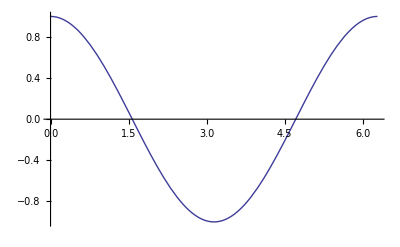

```mathematica
x0 = 1; x0p = 0;  tf = 2Pi; k=1; m=1;
xi=-10; xf=10;
(*V = Table[{x,x},{x,xi,xf}];*)
iV = Interpolation[V,InterpolationOrder->3];
orbit=NDSolve[{x''[t]+iV[x[t]]==0,
x[0]==x0,
x'[0]==x0p},
x,{t,0,tf}];
Plot[Evaluate[{x[t]}/.orbit],{t,0,tf}]
```